```mathematica
(*Set whatever directory the python script and abinit output file are in:*)
SetDirectory["/Users/Tommy/Documents/BU/CH 752 Computation Methods/abinit/Si/"]
(*Calls the python script on the file "tbase3_5o_DS2_EIG" and the second argument "print" will make it output the data to stdout so that it can be read by Mathematica. For some reason ReadList makes the list one level deeper, so the [[1]] at the end gets rid of that.*)
bandData=ReadList["!python Format-Band-Struct-Data-Print.py tbase3_5o_DS2_EIG print"][[1]];
```

/Users/Tommy/Documents/BU/CH 752 Computation Methods/abinit/Si

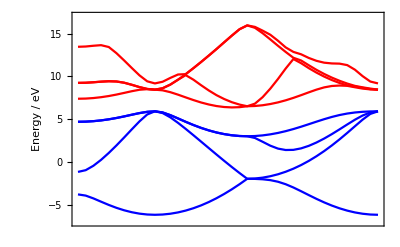

```mathematica
ListLinePlot[bandData[[All,2]]ᵀ(*take the transpose*),PlotRange->{{1,40},{-7,17}},Frame->True,FrameLabel->{"","Energy / eV"},FrameTicks->{{True,False},{False,False}},PlotStyle->{Blue,Blue,Blue,Blue,Red,Red,Red,Red},FrameStyle->Directive[Black,Medium]]
```

```mathematica
(*To export as a different format, just change the format of the output file name below here. The "%" refers to the last evaluated cell, so much sure the last thing you did was execute the plot.*)
Export["Si_band_struct.eps",%]
```

Si_band_struct.eps